```mathematica
Impedance[α0_,χ0_,U0_,θ0_,η0_,P0_]:=
Module[{α=α0,U=U0,P,rule,X,L,n,smoothingFunc,v,V,max,vacuum,plasma,u,hg,υ,ϵ,g,system,R,T,RP,Dissipation},
(*α - dissipation, α==ν/ω, ω->ω(1+ⅈα);
χ - dimensionless wave vector magnitude; χ=Subscript[k, 0] L, and L==v'[Subscript[x, 0]]^-1 where v[Subscript[x, 0]]==0;
U - anizatropy: p^2==4πe^2*n/m, b==eB/(mc), v==p^2/ω^2, u==b^2/ω^2, and with dissipation: v->v(1-ⅈα), u->U(1-ⅈα);
θ - angel between wave vector and XOY;
η - angle between wave vector projection and density gradient direction;
P - wave polarisation in native mode (O-X); 2d-vector*)

(*=====================================================================================================================*)
(*Natural plasma parameters,without dimensionlesses*)
Subscript[X, 0]=3;Subscript[V, max]=2;(*plasma boundary and depth; it makes reflection point equal to -Subscript[X, 0] √(1-1/Subscript[V, max]) for U==0*)
n=0.1;(*smoothing width, in parts of plasma whight*)
υ=Function[x,Subscript[V, max](1-x^2/Subscript[X, 0]^2)(*(2 Subscript[V, max] √(1-1/Subscript[V, max])x/Subscript[X, 0])*)];smoothingFunc=Function[x,(1+(x/Subscript[X, 0])^(2/n))^-1];
v=Function[x,υ[x]smoothingFunc[x](1-ⅈ α)];u=U(1-ⅈ α);
(*=====================================================================================================================*)
L=υ'[hg/.NSolve[υ[hg]==1(*-U*)&&-Subscript[X, 0]<hg<0,hg]⟦1⟧]^-1;(*For dimensionless*)
ϵ=Function[x,1-v[x L]/(1-u)];Subscript[ϵ, l]=Function[x,1-v[x L]];g=Function[x,(√u)/(1-u)v[x L]];
(*=====================================================================================================================*)
rule={Subscript[$k, 0]->χ0/L,$θ->θ0,$η->η0,$u->u,$X->Subscript[X, 0]/L,$ϵ->ϵ,Subscript[$ϵ, l]->Subscript[ϵ, l],$g->g};
Subscript[T, vp]=If[η0==0,Subscript[Υ, vp^s],Subscript[Υ, vp^r]]/.rule;
Subscript[T, pv]=If[η0==0,Subscript[Υ, pv^s],Subscript[Υ, pv^r]]/.rule;
P=Subscript[T, vp].P0;(*vacuum polarisation*)
system={eq,ic}/.rule;
Subscript[R, vacuum]=(Subscript[$R, general]/.NDSolve[system,{tt[x],st[x],ts[x],ss[x]},{x,-2 Subscript[X, 0] /L,2 Subscript[X, 0]/ L}])⟦1⟧;
RP=Subscript[R, vacuum].P/.x->-2 Subscript[X, 0]/L;
Dissipation=1-(Abs[RP⟦1⟧]^2+Abs[RP⟦2⟧]^2)/(Abs[P⟦1⟧]^2+Abs[P⟦2⟧]^2);
Subscript[R, plasma]=Subscript[T, pv].Subscript[R, vacuum].Subscript[T, vp];
{Dissipation,Subscript[R, plasma],Subscript[R, vacuum],Subscript[T, vp],Subscript[T, pv],Subscript[X, 0]/ L}
];
```

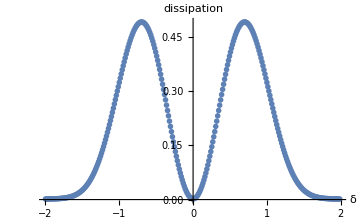

/Users/akutlin/Documents/private/VSHOPF/Egor/diplom/wolfram/results/isotropism/isotropism.csv

```mathematica
(*Isotropic dimensionless dissipation for X-wave; δ == χ^(1/3)Sin[θ] == (Subscript[k, 0] L)^(1/3)*Sin[θ]*)
δDissipation={};
χ=100;β=0;η=0;
δbegining=-2;δend=2;δnstep=300;
ProgressIndicator[Dynamic[(δ-δbegining)/(δend-δbegining)]]
For[δ=δbegining,δ<δend,δ+=(δend-δbegining)/δnstep,
δDissipation=Append[δDissipation,{δ,Impedance[10^-5,χ,(β*χ^(-2/3))^2,ArcSin[δ*χ^(-1/3)],η,{0,1}]⟦1⟧}];
];
ListPlot[δDissipation,PlotRange->Full,AxesLabel->{"δ","dissipation"},ImageSize->Medium]
SaveData[config["isotropism","data"],δDissipation]
Clear[χ,β,δ,η,δbegining,δend,δnstep];
```

```mathematica
(*Anisotropic dimensionless dissipation for X-wave, η == 0; δ == χ^(1/3)Sin[θ] == (Subscript[k, 0] L)^(1/3)*Sin[θ], β == χ^(2/3)√u*)
δβDissipation={};
χ=100;
δbegining=-2;δend=2;δnstep=100;
βbegining =0; βend = 1; βnstep = 100;
ProgressIndicator[Dynamic[(β-βbegining)/(βend-βbegining)+((βend-βbegining)/βnstep)*(δ-δbegining)/(δend-δbegining)]]
For[β=βbegining,β<βend,β+=(βend-βbegining)/βnstep,
For[δ=δbegining,δ<δend,δ+=(δend-δbegining)/δnstep,
δβDissipation=Append[δβDissipation,{δ,β,Impedance[10^-5,χ,(β*χ^(-2/3))^2,ArcSin[δ*χ^(-1/3)],0,{0,1}]⟦1⟧}];
];
];
ListPlot3D[δβDissipation,PlotRange->Full,AxesLabel->{"δ","β","dissipation"}]
SaveData[config["teta","data"],δβDissipation]
Clear[χ,δ,β,δβDissipation,δbegining,δend,δnstep,βbegining,βend,βnstep];
```

-Graphics3D-

/Users/akutlin/Documents/private/VSHOPF/Egor/diplom/wolfram/results/teta/teta.csv

```mathematica
(*Anisotropic dimensionless dissipation for O-wave, θ == 0; σ == (2 √2 Subscript[πχ, 0] u^(1/4))^(-1/2)*)
ηχDissipation={};
σ=0.07;
χbegining=(2 √2 π σ^2)^-1+1;χend=(2 √2 π σ^2)^(-3/2)-1;χnstep=10;ηnstep = 50;
ProgressIndicator[Dynamic[(χ-χbegining)/(χend-χbegining)]]
For[χ=χbegining,χ<χend,χ+=(χend-χbegining)/χnstep,
υ=(2 √2 π χ σ^2)^-4;H=ArcSin[√(√υ/(1+√υ))];ηbegining=H-3σ;ηend=H+3σ;
For[η=ηbegining,η<ηend,η+=(ηend-ηbegining)/ηnstep,
AppendTo[ηχDissipation,{(η-H)/σ,χ,Impedance[10^-5,χ,υ,0,η,{1,0}]⟦1⟧}];
];
];
ListPlot3D[ηχDissipation,PlotRange->Full,AxesLabel->{"δη/σ","χ","dissipation"}]
SaveData[config["eta","data"],ηχDissipation]
Clear[ηχDissipation,χ,σ,η,H,υ,χbegining,χend,χnstep,ηnstep,ηbegining,ηend,experiment,theory,result];
```

-Graphics3D-

/Users/akutlin/Documents/private/VSHOPF/Egor/diplom/wolfram/results/eta/eta.csv

```mathematica
(*Anisotropic dimensionless dissipation for O-wave, θ == 0; σ == (2 √2 Subscript[πχ, 0] u^(1/4))^(-1/2)*)
ηχDissipation={};
σ=0.07;
χbegining=(2 √2 π σ^2)^(-3/2)-1;χend=500;χnstep=10;ηnstep = 50;
ProgressIndicator[Dynamic[(χ-χbegining)/(χend-χbegining)]]
For[χ=χbegining,χ<χend,χ+=(χend-χbegining)/χnstep,
υ=(2 √2 π χ σ^2)^-4;H=ArcSin[√(√υ/(1+√υ))];ηbegining=H-3σ;ηend=H+3σ;
For[η=ηbegining,η<ηend,η+=(ηend-ηbegining)/ηnstep,
AppendTo[ηχDissipation,{(η-H)/σ,χ,Impedance[10^-5,χ,υ,0,η,{1,0}]⟦1⟧}];
];
];
ListPlot3D[ηχDissipation,PlotRange->Full,AxesLabel->{"δη/σ","χ","dissipation"}]
(*SaveData[config["eta","data"],ηχDissipation]*)
Clear[ηχDissipation,χ,σ,η,H,υ,χbegining,χend,χnstep,ηnstep,ηbegining,ηend,experiment,theory,result];
```

-Graphics3D-

```mathematica
αϕDissipation={};
αbegining=-π;αend=π;αnstep=100;
ϕbegining=-π;ϕend=π;ϕnstep=100;
ProgressIndicator[Dynamic[(α-αbegining)/(αend-αbegining)]]
For[α=αbegining,α<αend,α+=(αend-αbegining)/αnstep,
For[ϕ=ϕbegining,ϕ<ϕend,ϕ+=(ϕend-ϕbegining)/ϕnstep,
P={Sin[ϕ],Cos[ϕ] ⅇ^(ⅈ α)};
SubPlus[V]=U.P;
SubMinus[V]=R.SubPlus[V];
AppendTo[αϕDissipation,{α,ϕ,1-(Abs[SubMinus[V]⟦1⟧]^2+Abs[SubMinus[V]⟦2⟧]^2)/(Abs[SubPlus[V]⟦1⟧]^2+Abs[SubPlus[V]⟦2⟧]^2)}];
];
];
Clear[α,ϕ,P,V];

ListContourPlot[αϕDissipation,PlotRange->Full,AxesLabel->{α,ϕ,dissipation},PlotLegends->Automatic,PlotTheme->"Monochrome"]
```

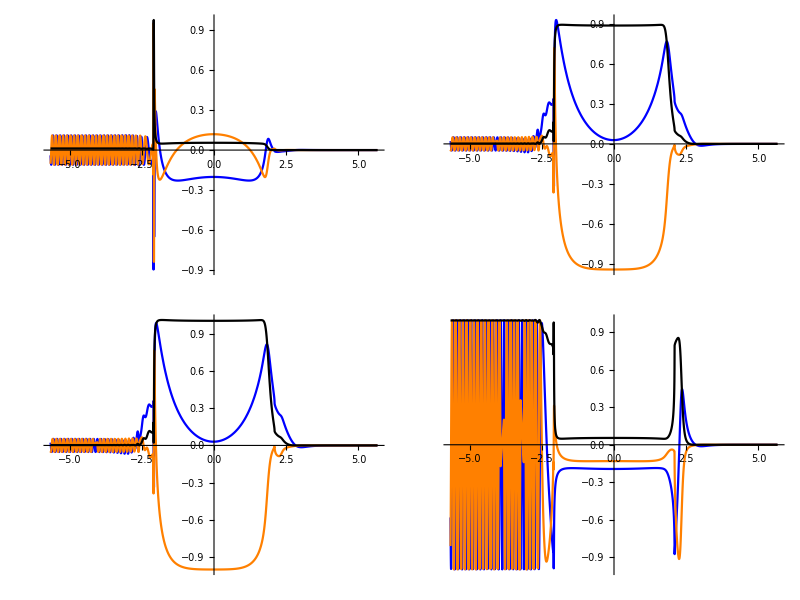
{0.985302,(-Graphics-)}

```mathematica
χ=30;υ=0.1;η=0.5;θ=0;(*ArcSin[√((√υ)/(1+√υ))]*)
Impedance[10^-5,χ,υ,θ,η,{1,0}];
{%⟦1⟧,Table[Plot[{Re[%⟦2⟧⟦i,j⟧],Im[%⟦2⟧⟦i,j⟧],Abs[%⟦2⟧⟦i,j⟧]^2},{x,-2%⟦6⟧,2%⟦6⟧},ImageSize->Medium,PlotRange->Full,PlotStyle->{Blue,Orange,Black}],{i,1,2},{j,1,2}]//MatrixForm}
R=%%⟦3⟧/.x->-2%%⟦6⟧;
U=%%%⟦4⟧;
Clear[χ,υ,θ,η]
```